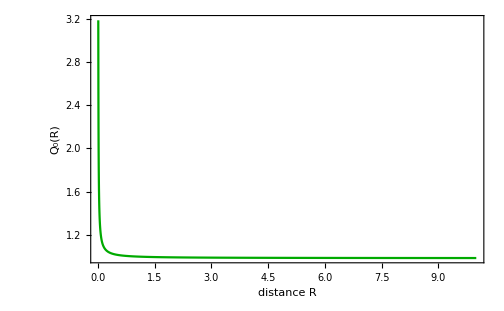

```mathematica
Clear[k,m,ss,om,jj];(*m1r=k r^3; m2r=m; msr= 4 Pi ss r^2;*)
k=0;
m=1;
om=0;  (* ω *)
jj=0;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01/x^2;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0a=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2a=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2;
q4a=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f2s=Plot[q0a,{x,0.01,10},Frame->True,FrameLabel->{"distance R"," Q_0(R)"},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},PlotRange->All,Axes->False]
```

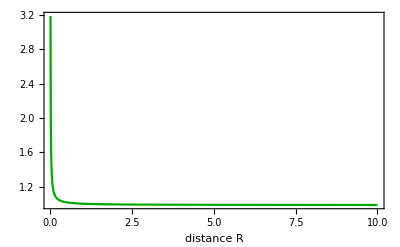

```mathematica
f20=Plot[q0a,{x,0.01,10},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False,PlotRange->All]
```

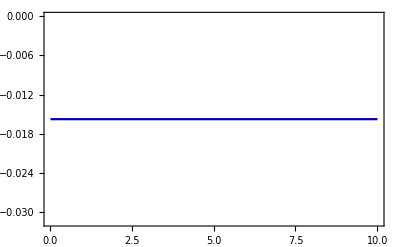

```mathematica
f2a=Plot[q2a,{x,0.03,10},Frame->True,PlotStyle->{Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

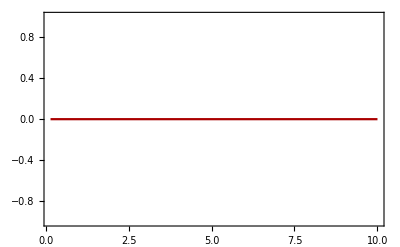

```mathematica
f2b=Plot[q4a,{x,0.15,10},Frame->True,PlotStyle->{Darker[Red]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

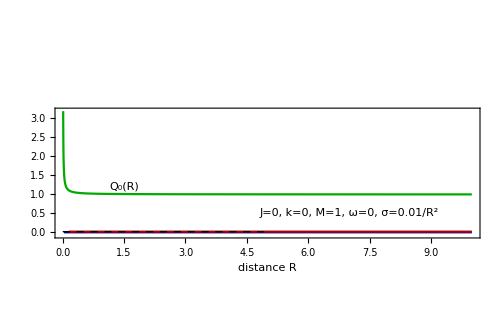

```mathematica
fig1a=Show[f20,f2a,f2b, Graphics[{Inset[Framed["J=0, k=0, M=1, ω=0, σ=0.01/R^2"],{7,0.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{2.9,30},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset["2.25",{2.25,-1},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{1.5,1.2},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{2.7,60},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{5,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-0.1,3.2}]
```

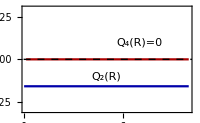

```mathematica
fd01smallc=Show[f2a,f2b,Graphics[{Inset["Q_2(R)",{5,-0.01},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)=0",{7,0.01},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Medium,Italic,FontFamily->"Times",12},ImageSize->200,PlotRange->{{0.1,10},{-0.03,0.03}},Axes->False]
```

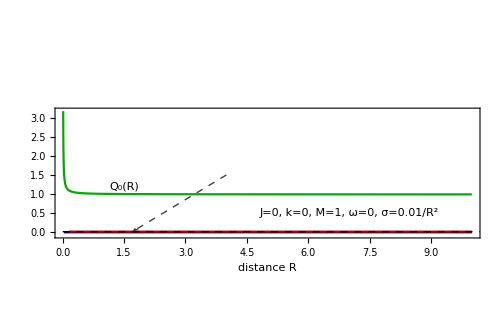

```mathematica
fig12=Show[fig1a,Epilog->{Inset[fd01smallc,Scaled[{0.5,0.7}]],Dashed,Darker[Gray,0.5],Arrowheads[Medium],Arrow[{{4,1.5},{1.7,0}}],{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Bold,Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large]]
```

```mathematica
Export["D:fig12.pdf",fig12,"PDF"];
Export["D:fig12.eps", fig12];
```

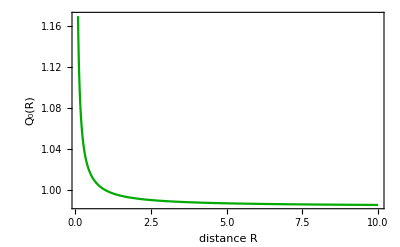

```mathematica
Clear[k,m,ss,om,jj];(*m1r=k r^3; m2r=m; msr= 4 Pi ss r^2;*)
k=0;
m=1;
om=0.1;  (* ω *)
jj=0.001;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01/x^2;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0a=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2a=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2;
q4a=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f2sb=Plot[q0a,{x,0.085,10},Frame->True,FrameLabel->{"distance R"," Q_0(R)"},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},PlotRange->All,Axes->False]
```

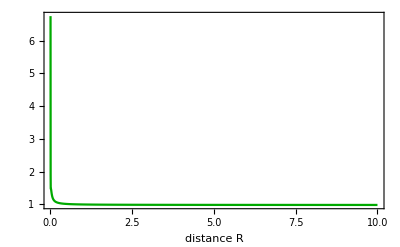

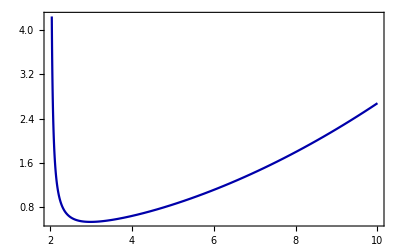

```mathematica
f20b=Plot[q0a,{x,0.007,10},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False,PlotRange->All]
f2ab=Plot[q2a,{x,2.01,10},Frame->True,PlotStyle->{Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

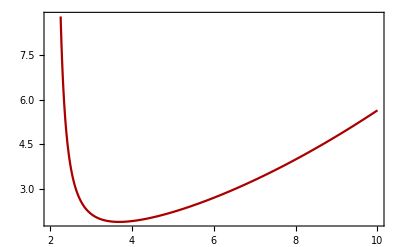

```mathematica
f2bb=Plot[q4a,{x,2.01,10},Frame->True,PlotStyle->{Darker[Red]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

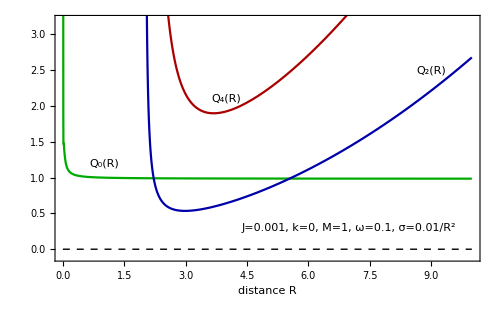

```mathematica
fig1ab=Show[f20b,f2ab,f2bb, Graphics[{Inset[Framed["J=0.001, k=0, M=1, ω=0.1, σ=0.01/R^2"],{7,0.3},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{9,2.5},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{1,1.2},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{4,2.1},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{10,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-0.1,3.2}]
```

```mathematica
Export["D:fig1ab.pdf",fig1ab,"PDF"];
Export["D:fig1ab.eps", fig1ab];
```